```mathematica
(* Computer Graphics with Applications *)
```

```mathematica
(* Lecture 4. 3D Graphics-2. Lists. Tables. 3D Primitives *)
```

```mathematica
SetOptions[{Plot,Plot3D,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot, Graphics , Graphics3D,SphericalPlot3D,DensityPlot,DensityPlot3D,ContourPlot,SliceContourPlot3D,SliceDensityPlot3D,RegionPlot,RegionPlot3D,Graphics3D,RevolutionPlot3D},ImageSize->Medium];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
(* 3D graphic tools-  continued. Surfaces of revolution *)
```

```mathematica
(* Cylinder  *)
```

```mathematica
x[t_]:=1
```

```mathematica
y[t_]:=t
```

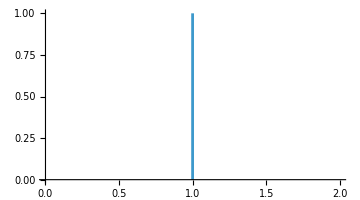

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,1}]
```

```mathematica
RevolutionPlot3D[ {x[t],y[t]},{t,0,2Pi},BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Cone  *)
```

```mathematica
Clear[x,y,R]
```

```mathematica
x[t_]:=t  (* ก็มีค่าเหมือน y=x *)
```

```mathematica
y[t_]:=t
```

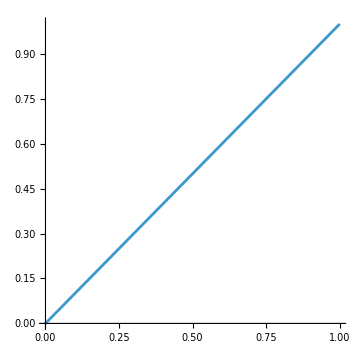

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,1}]
```

```mathematica
RevolutionPlot3D[ {x[t],y[t]},{t,0,2Pi},BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Axes from the origin  *)
```

```mathematica
RevolutionPlot3D[ {x[t],y[t]},{t,0,2Pi},BoxRatios->1,AxesOrigin->{0,0,0},AxesStyle->Black]
```

-Graphics3D-

```mathematica
(* Torus  *)
```

```mathematica
(* The base function: a circle with the radius R and the center at {x0,y0}
x[t_]:=R Cos[t]+x0
   y[t_]:=R Sin[t]+y0 
(memorize)
 *)
```

```mathematica
Clear[x,y,R]
```

```mathematica
R=0.25
```

0.25

```mathematica
x0=0.5
```

0.5

```mathematica
y0=-1
```

-1

```mathematica
x[t_]:=R Cos[t]+x0
```

```mathematica
y[t_]:=R Sin[t]+y0
```

```mathematica
fCir1[t_]:={x[t],y[t]}
```

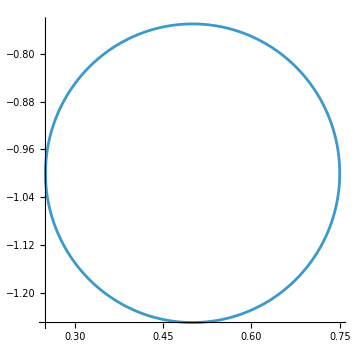

```mathematica
Circle1=ParametricPlot[fCir1[t],{t,0,2Pi}]
```

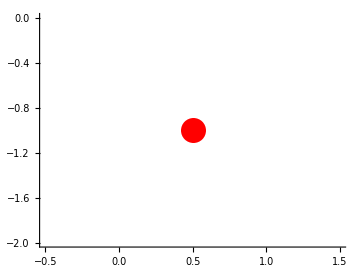

```mathematica
Center1=Graphics[{Red,PointSize[0.05], Point[{x0,y0}]},Axes->True]
```

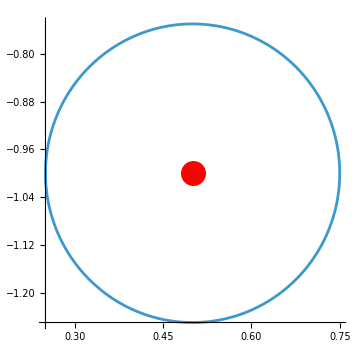

```mathematica
Show[Circle1, Center1]
```

```mathematica
Torus1=RevolutionPlot3D[ {x[t],y[t]},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
Torus2=RevolutionPlot3D[ {x[t],y[t]},{t,0,Pi}] (* ถ้าเป็นแค่ Pi ล่ะ *)
```

-Graphics3D-

```mathematica
Torus1=RevolutionPlot3D[ {x[t],y[t]},{t,0,2Pi}, {s, 0, Pi}] (* ถ้าไม่ set ข้างหลัง default จะเป็น 2Pi *)
```

-Graphics3D-

```mathematica
PlaneX0[y_,z_]:={0,y,z}
```

```mathematica
GPX0=ParametricPlot3D[PlaneX0[y,z],{y,-1,1},{z,-2,2},PlotStyle->{Gray,Opacity[0.7]},Mesh->None]
```

-Graphics3D-

```mathematica
Show[{Torus1,GPX0}]
```

-Graphics3D-

```mathematica
(* The 3D circle in the plane x=0 *)
```

```mathematica
Cir3D[t_]:={0,x[t],y[t]}
```

```mathematica
GCir3D=ParametricPlot3D[Cir3D[t],{t,0,2Pi},PlotStyle->{Purple,Thickness[0.025]}]
```

-Graphics3D-

```mathematica
Show[{Torus1,GPX0,GCir3D},ImageSize->Medium]
```

-Graphics3D-

```mathematica
(* 2D Plots to show 3D objects  *)
```

```mathematica
(* A Density Plot shows the height of the surface in the z direction by the color intensity *)
```

```mathematica
fe[x_,y_]:=Exp[Sin[x*y]]
```

```mathematica
Gdensity1=DensityPlot[fe[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
(* Compare *)
```

```mathematica
Gsurplot1=Plot3D[fe[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(* This arranges the graphs in the graphic row *)
```

^4

```mathematica
Show[GraphicsRow[{Gdensity1,Gsurplot1}]]
```

-Graphics-

```mathematica
(* ContourPlot generates a contour plot of f[x_,y_] *)
```

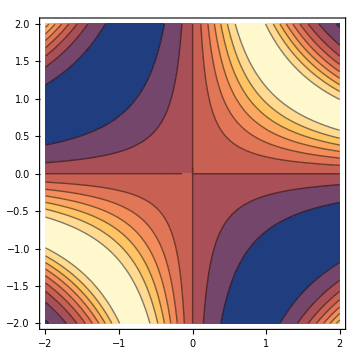

```mathematica
Gcontour1=ContourPlot[fe[x,y],{x,-2,2},{y,-2,2}]
```

```mathematica
Show[GraphicsRow[{Gdensity1,Gsurplot1,Gcontour1}]]
```

-Graphics-

```mathematica
(* Note the option Contours-> *)
```

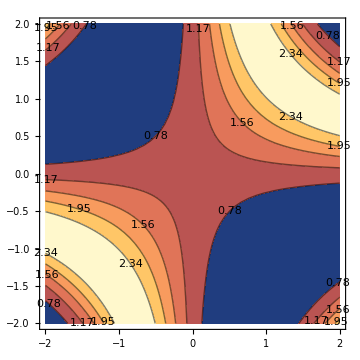

```mathematica
Gcontour12=ContourPlot[fe[x,y],{x,-2,2},{y,-2,2},Contours->5,ContourLabels->True]
```

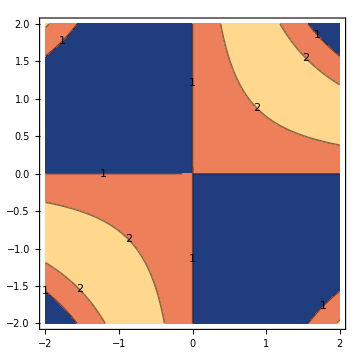

```mathematica
Gcontour13=ContourPlot[fe[x,y],{x,-2,2},{y,-2,2},Contours->{1,2,5},ContourLabels->True]
```

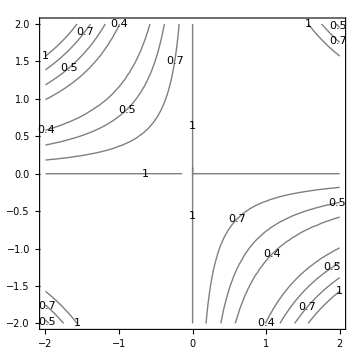

```mathematica
Gcontour14=ContourPlot[fe[x,y],{x,-2,2},{y,-2,2},Contours->{1,0.5,0.4,0.7},ContourLabels->True,ContourShading->False]
```

```mathematica
(* SliceContourPlot3D combines Plot3D and ContourPlot in 3D (maps onto the x,y=plane)*)
```

```mathematica
Gslice1=SliceContourPlot3D[fe[x,y],z==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
(* This superposition always looks nice *)
```

```mathematica
Show[{Gslice1,Gsurplot1},PlotRange->{Automatic,Automatic,{0,3}}]
```

-Graphics3D-

```mathematica
(* Similarly: SliceDensityPlot3D combines Plot3D and DensityPlot in 3D *)
```

```mathematica
GsliceD1=SliceDensityPlot3D[fe[x,y],z==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
Show[{GsliceD1,Gsurplot1},PlotRange->{Automatic,Automatic,{0,3}}]
```

-Graphics3D-

```mathematica
Clear[S4]
```

```mathematica
(* Self study: a similar plot is can be generated for a parametric surface as follows  *)
```

```mathematica
x4[a_,b_]:=Cos[b] (6-(5/4+Sin[3 a]) Sin[a-3 b])
```

```mathematica
y4[a_,b_]:=(6-(5/4+Sin[3 a]) Sin[a-3 b]) Sin[b]
```

```mathematica
z4[a_,b_]:= -Cos[a-3 b] (5/4+Sin[3 a])
```

```mathematica
S4[u_,v_]:={x4[u,v],y4[u,v],z4[u,v]}
```

```mathematica
G1=ParametricPlot3D[S4[u,v],{u,0,2Pi},{v,0, 2 Pi},PlotStyle->Yellow,  PlotRange->{{-10,10},{-10,10},{-5,2}}]
```

-Graphics3D-

```mathematica
(* Change the function z4 (flatten the surface S4 and move it down by d units)  *)
```

```mathematica
d=5.0
```

5.

```mathematica
z4flat[a_,b_]:= -Cos[a-3 b] (5/4+Sin[3 a])0.01-d
```

```mathematica
S4flat[u_,v_]:={x4[u,v],y4[u,v],z4flat[u,v]}
```

```mathematica
G2flat=ParametricPlot3D[S4flat[u,v],{u,0,2Pi},{v,0, 2 Pi},PlotStyle->Brown,MeshStyle->Yellow]
```

-Graphics3D-

```mathematica
Show[{G1,G2flat}]
```

-Graphics3D-

```mathematica
(* Self-study. Needs Math3. The normal to the parametric surface S(u,v) is given by (∂S)/(∂u)x(∂S)/(∂u)/|(∂S)/(∂u)x(∂S)/(∂u)| , where x denotes the cross product. Difficult? Mathematica performs the symbolic calculations for us *)
```

```mathematica
(* Define Sf[u_,v_]:={u,v,u^2-v^2} *)
```

```mathematica
Sf[u_,v_]:={u,v,u^2-v^2}
```

```mathematica
GSf=ParametricPlot3D[Sf[u,v],{u,-1,1},{v,-1,1},BoxRatios->1]
```

-Graphics3D-

```mathematica
(* The normal *)
```

```mathematica
N1=Cross[D[Sf[u,v],u],D[Sf[u,v],v]]
```

{-2 u,2 v,1}

```mathematica
(* Normalize *)
```

```mathematica
Norm[N1]
```

√(1+4 Abs[u]^2+4 Abs[v]^2)

```mathematica
(* Cut and paste here  *)
```

```mathematica
NV[u_,v_]:={-2 u,2 v,1}/√(1+4 Abs[u]^2+4 Abs[v]^2)
```

```mathematica
(* Check *)
```

```mathematica
NV[0.5,0.1]
```

{-0.70014,0.140028,0.70014}

```mathematica
(* This is the direction vector. The line equation is then NV t+p, where p is the required point  *)
```

```mathematica
p=Sf[0.5,0.1]
```

{0.5,0.1,0.24}

```mathematica
(* Plot the normal to S[u,v] from the point [u,v]=0.5,0.1 *)
```

```mathematica
LNorm[t_]:=NV[0.5,0.1] t +p
```

```mathematica
(* Check *)
```

```mathematica
LNorm[t]
```

{0.5-0.70014 t,0.1+0.140028 t,0.24+0.70014 t}

```mathematica
Arrow1=Arrow[{LNorm[0],LNorm[1]}]
```

Arrow[{{0.5,0.1,0.24},{-0.20014,0.240028,0.94014}}]

```mathematica
(* Check *)
```

```mathematica
NormalSf=Graphics3D[{Thickness[0.02],Arrow1},BoxRatios->1]
```

-Graphics3D-

```mathematica
Show[{GSf,NormalSf}]
```

-Graphics3D-

```mathematica
(* To build up  3D graphics recall the idea of the Lists and introduce Tables - one of the most important ways to generate lists  *)
```

```mathematica
(* Numerical lists  *)
```

```mathematica
(* 1D List- vector  *)
```

```mathematica
v1={1,2,5,6,7}
```

{1,2,5,6,7}

```mathematica
(* List of 2D points  *)
```

```mathematica
MP={{1,2},{2,3},{3,4},{7,8}}
```

{{1,2},{2,3},{3,4},{7,8}}

```mathematica
(* This can be used in the 2D Plot *)
```

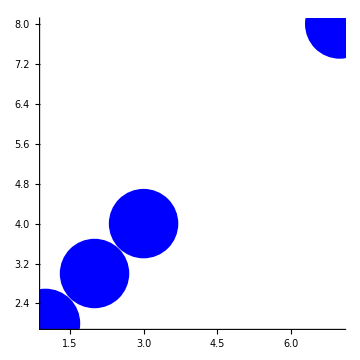

```mathematica
G2D=Graphics[{Blue,PointSize[0.15],Point[MP]},Axes->True]
```

```mathematica
(* Extract a 3D element from v1 *)
```

```mathematica
v1[[3]]
```

5

```mathematica
(* Length of v1 *)
```

```mathematica
Length[v1]
```

5

```mathematica
(* 2D List- matrix  *)
```

```mathematica
M1={{1,2,3},{2,3,4},{3,4,5},{7,8,9}}
```

{{1,2,3},{2,3,4},{3,4,5},{7,8,9}}

```mathematica
MatrixForm[M1]
```

(1 | 2 | 3
2 | 3 | 4
3 | 4 | 5
7 | 8 | 9)

```mathematica
(* Dimensions of M1 *)
```

```mathematica
Dimensions[M1]
```

{4,3}

```mathematica
(* Transpose*)
```

```mathematica
M1T=Transpose[M1]
```

{{1,2,3,7},{2,3,4,8},{3,4,5,9}}

```mathematica
MatrixForm[M1T]
```

(1 | 2 | 3 | 7
2 | 3 | 4 | 8
3 | 4 | 5 | 9)

```mathematica
Dimensions[M1T]
```

{3,4}

```mathematica
(* Extract  row 1*)
```

```mathematica
M1[[1]]
```

{1,2,3}

```mathematica
(* Extract  column 2*)
```

```mathematica
Transpose[M1][[2]]
```

{2,3,4,8}

```mathematica
(* Extract  row 2, col3 *)
```

```mathematica
M1[[2]][[3]]
```

4

```mathematica
(* General list with sublists with the different size  *)
```

```mathematica
M2={{1,2,3,5,6},{2,3,4},{3,4}}
```

{{1,2,3,5,6},{2,3,4},{3,4}}

```mathematica
(* General list with different elements: 1)number, 2)string, 3) sublist, 4) image *)
```

```mathematica
GL={991,"this is a string", {1,2}, G2D}
```

{991,this is a string,{1,2},-Graphics-}

```mathematica
GL[[2]]
```

this is a string

```mathematica
GL[[4]]
```

-Graphics-

```mathematica
(* Constructing 1D lists: Range *)
```

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[2,7]
```

{2,3,4,5,6,7}

```mathematica
Range[1,10,3]
```

{1,4,7,10}

```mathematica
L1=Range[0,5,0.25]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
(* This is similar to Array f[x_]:=x *)
```

```mathematica
Clear[fxx]
```

```mathematica
fxx:=1.0#1&
```

```mathematica
L1A=Array[fxx,21,{0,5.}]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
(* Constructing 2D lists with Range *)
```

```mathematica
L2=Range[0,10,Range[2]]
```

{{0,1,2,3,4,5,6,7,8,9,10},{0,2,4,6,8,10}}

```mathematica
(* Table : 1D *)
```

```mathematica
T1=Table[i^2+i,{i,10}]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
T2=Table[i^2+i,{i,3,10}]
```

{12,20,30,42,56,72,90,110}

```mathematica
T3=Table[i^2+i,{i,3,10,0.5}]
```

{12.,15.75,20.,24.75,30.,35.75,42.,48.75,56.,63.75,72.,80.75,90.,99.75,110.}

```mathematica
(* Table of functions *)
```

```mathematica
Tf=Table[x^n+1,{n,3}]
```

{1+x,1+x^2,1+x^3}

```mathematica
(* Plot the table of functions *)
```

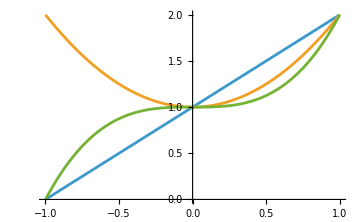

```mathematica
Plot[Tf,{x,-1,1}]
```

```mathematica
(* Table of Random Colors *)
```

```mathematica
ListColors=Table[RandomColor[],{i,5}]
```

{RGBColor[0.48630236632888924, 0.6247568743682343, 0.6356673252827749],RGBColor[0.44753151279852754, 0.7419206771839773, 0.6274810632665277],RGBColor[0.21355897965094717, 0.683688587808557, 0.185073991595897],RGBColor[0.7552199545367753, 0.7452060755810226, 0.14418179074507198],RGBColor[0.7796908728960075, 0.5321164608400144, 0.7646576373262077]}

```mathematica
(* Table of graphs with different color *)
```

```mathematica
ft[t_]:=Sin[t^2]
```

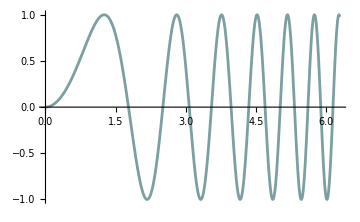
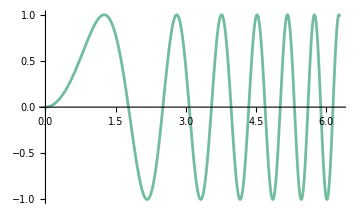
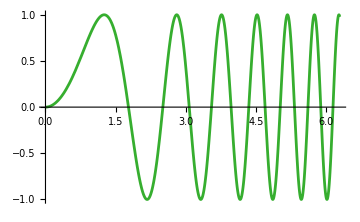
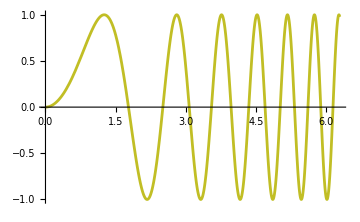
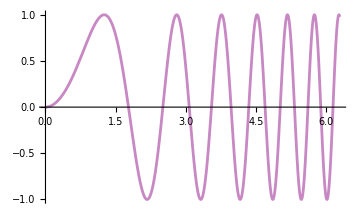

```mathematica
TG=Table[Plot[ft[t],{t,0,2Pi}, PlotStyle->C],{C,ListColors}]
```

```mathematica
(* Output graph 2 and 5 *)
```

```mathematica
{TG[[2]],TG[[5]]}
```

{-Graphics-,-Graphics-}

```mathematica
(* Or  *)
```

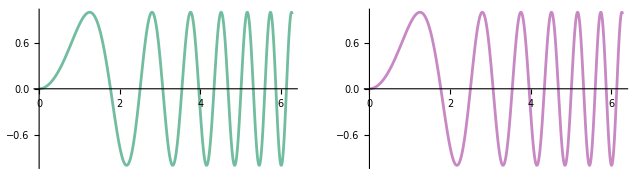

```mathematica
GraphicsRow[{TG[[2]],TG[[5]]}]
```

```mathematica
(* Read 1D Data into a list and plot it using 1) ListPlot  2) Graphics/Point: compare *)
```

```mathematica
SetDirectory["/Users/npwitk/Library/Mobile Documents/com~apple~CloudDocs/School/Undergraduate Degree (SIIT) Archive/Year 2/Second Semester/CSS221 - Computer Graphics and Applications/CSS221-Computer-Graphics-and-Applications/Lecture/Lecture 4"]
```

/Users/npwitk/Library/Mobile Documents/com~apple~CloudDocs/School/Undergraduate Degree (SIIT) Archive/Year 2/Second Semester/CSS221 - Computer Graphics and Applications/CSS221-Computer-Graphics-and-Applications/Lecture/Lecture 4

```mathematica
Largedata:=Import["experiment.txt","List"]
```

```mathematica
NP=Length[Largedata]
```

50

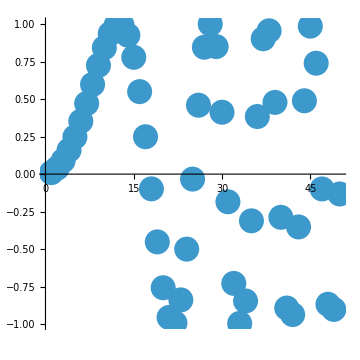

```mathematica
ListPlot[Largedata,PlotStyle->PointSize[0.05],AspectRatio->1]
```

```mathematica
LargedataXY:=Table[{i,Largedata[[i]]},{i,Length[Largedata]}]
```

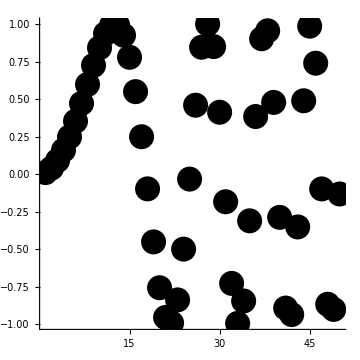

```mathematica
Graphics[{PointSize[0.05],Point[LargedataXY]},AspectRatio->1,Axes->True]
```

```mathematica
(* 3D primitives. If the time allows. *)
```

```mathematica
(* Example 0 Plot  p1={1,1,1} Red, p2={1,2,2} Green and p3=p1+p2 Blue *)
```

```mathematica
p1={1,1,1}
```

{1,1,1}

```mathematica
p2={1,2,2}
```

{1,2,2}

```mathematica
p3=p1+p2
```

{2,3,3}

```mathematica
Listp1p2={p1,p2,p3}
```

{{1,1,1},{1,2,2},{2,3,3}}

```mathematica
Colors12={Red,Green,Blue}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

```mathematica
Points12=Point[{p1,p2,p3},VertexColors-> Colors12]
```

Point[{{1,1,1},{1,2,2},{2,3,3}},VertexColors→{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}]

```mathematica
Graphics3D[{PointSize[0.05],Points12},PlotRange->3.2,Axes->True]
```

-Graphics3D-

```mathematica
(* By default, M13 draws 3D axes on the box. To change it use AxesOrigin-> *)
```

```mathematica
G3points=Graphics3D[{PointSize[0.05],Points12},PlotRange->3.2,Axes->True, AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
(* Example 1 Create 10 random points in the range -5,5 in x,y, and z. Plot them in 3D *)
```

```mathematica
fRandom3D[]:={0.5-Random[],0.5-Random[],0.5-Random[]}
```

```mathematica
P10=Table [fRandom3D[],{i,10}]
```

{{0.167325,-0.425427,-0.291124},{-0.0856092,-0.0736753,-0.23655},{0.108555,0.385061,-0.242779},{-0.392222,-0.210278,-0.0677348},{-0.0714911,0.126709,-0.212361},{-0.0958833,-0.482326,-0.345685},{0.222366,0.251192,0.473125},{-0.432738,-0.4709,-0.472697},{-0.1942,0.492688,0.320224},{0.112912,0.379475,0.229238}}

```mathematica
Points10=Point[P10]
```

Point[{{0.167325,-0.425427,-0.291124},{-0.0856092,-0.0736753,-0.23655},{0.108555,0.385061,-0.242779},{-0.392222,-0.210278,-0.0677348},{-0.0714911,0.126709,-0.212361},{-0.0958833,-0.482326,-0.345685},{0.222366,0.251192,0.473125},{-0.432738,-0.4709,-0.472697},{-0.1942,0.492688,0.320224},{0.112912,0.379475,0.229238}}]

```mathematica
Lines10=Line[P10]
```

Line[{{0.167325,-0.425427,-0.291124},{-0.0856092,-0.0736753,-0.23655},{0.108555,0.385061,-0.242779},{-0.392222,-0.210278,-0.0677348},{-0.0714911,0.126709,-0.212361},{-0.0958833,-0.482326,-0.345685},{0.222366,0.251192,0.473125},{-0.432738,-0.4709,-0.472697},{-0.1942,0.492688,0.320224},{0.112912,0.379475,0.229238}}]

```mathematica
GP10=Graphics3D[{{Red,PointSize->0.05,Points10},Lines10},Axes->True]
```

-Graphics3D-

```mathematica
(* 3D Primitives are given below. They require the wrapper Graphics3D[] The most important are Line, Point and  *)
```

```mathematica
(* -Graphics-*) 
(* -Graphics-*)
```

```mathematica
(* The most important are Line, Point Arrow and Polygon *)
```

-Graphics-

```mathematica
(* Plotting the space curves by 3D primitives and wrappers *)
```

```mathematica
(* Define the spiral *)
```

```mathematica
x[t_]:=R Sin[t]
```

```mathematica
y[t_]:=R Cos[t]
```

```mathematica
z[t_]:=t
```

```mathematica
S[t_]:={x[t],y[t],z[t]}
```

```mathematica
(* Define 50 points on the interval [0,10] *)
```

```mathematica
Clear[fx]
```

```mathematica
fx[x_]:=1.0 x
```

```mathematica
P50=Array[fx,50,{0,10}]
```

{0.,0.204082,0.408163,0.612245,0.816327,1.02041,1.22449,1.42857,1.63265,1.83673,2.04082,2.2449,2.44898,2.65306,2.85714,3.06122,3.26531,3.46939,3.67347,3.87755,4.08163,4.28571,4.4898,4.69388,4.89796,5.10204,5.30612,5.5102,5.71429,5.91837,6.12245,6.32653,6.53061,6.73469,6.93878,7.14286,7.34694,7.55102,7.7551,7.95918,8.16327,8.36735,8.57143,8.77551,8.97959,9.18367,9.38776,9.59184,9.79592,10.}

```mathematica
(* Generate a discrete set of points on the spiral  *)
```

```mathematica
P50S=Map[S,P50];
```

```mathematica
(* Plot   *)
```

```mathematica
Points50=Point[P50S];
```

```mathematica
Lines50=Line[P50S];
```

```mathematica
GP50S=Graphics3D[{{Red,PointSize->0.05,Points50},Lines50},Axes->True,BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Plot with a title *)
```

```mathematica
P50S[[50]]
```

{-0.136005,-0.209768,10.}

```mathematica
GP50ST=Graphics3D[Text["My spiral",P50S[[50]]],BoxRatios->1]
```

-Graphics3D-

```mathematica
Show[GP50S,GP50ST]
```

-Graphics3D-

```mathematica
T1=Style["My spiral",Large,Bold,Blue]
```

My spiral

```mathematica
GP50ST1=Graphics3D[Text[T1,P50S[[50]]],BoxRatios->1]
```

-Graphics3D-

```mathematica
Show[GP50S,GP50ST1]
```

-Graphics3D-

```mathematica
(* Polygons and other objects  *)
```

-Graphics-

```mathematica
(* Example 01 Triangle *)
```

```mathematica
Plist1={{1,0,0},{1,1,1},{0,0,1}}
```

{{1,0,0},{1,1,1},{0,0,1}}

```mathematica
pol1=Polygon[Plist1];
```

```mathematica
Graphics3D[{Pink,pol1}]
```

-Graphics3D-

```mathematica
(* Example 02 Self study: EdgeForm to specify that edges of polygons. *)
```

```mathematica
Plist2={{1,0,0},{1,1,1},{1,2.5,1},{0,0,1}}
```

{{1,0,0},{1,1,1},{1,2.5,1},{0,0,1}}

```mathematica
pol2=Polygon[Plist2];
```

```mathematica
{Graphics3D[{Pink,pol2}],Graphics3D[{EdgeForm[Thick],Pink,pol1}],Graphics3D[{EdgeForm[Thick],EdgeForm[Dashed],Pink,Opacity[0.5],pol1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Vertex colors *)
```

```mathematica
ColorList3={Red,Green,Blue,Yellow}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0]}

```mathematica
pol3=Polygon[Plist2, VertexColors->ColorList3]
```

Polygon[…]

```mathematica
Graphics3D[pol3]
```

-Graphics3D-

```mathematica
(* Other primitives: Cylinder Sphere, Cuboid, Cone, Spheroid *)
```

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2},1.5],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

-Graphics3D-

```mathematica
(* We will practice these functions at the Lab *)
```

```mathematica
(* Self study: RegionPlot, RegionPlot3D: Plot a region defined by an inequality. (if time allows) *)
```

```mathematica
Clear[R]
```

```mathematica
R=2.5^2
```

6.25

```mathematica
(* Circle with the radius 2.5 *)
```

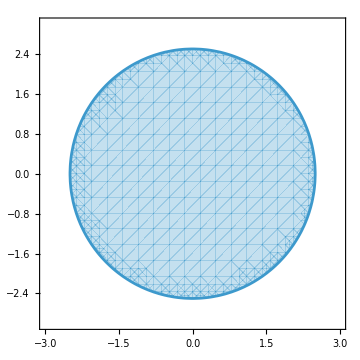

```mathematica
RegionPlot[x^2+y^2<R,{x,-3,3},{y,-3,3}]
```

```mathematica
(* Plot several regions with the legends *)
```

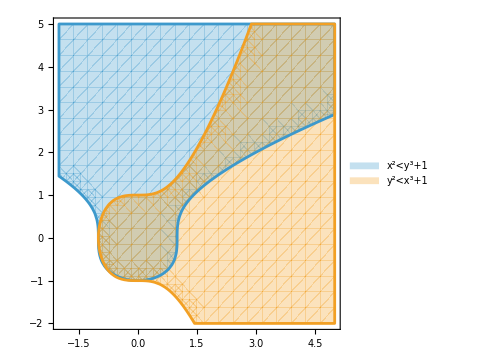

```mathematica
RegionPlot[{x^2<y^3+1,y^2<x^3+1},{x,-2,5},{y,-2,5},PlotLegends->"Expressions"]
```

```mathematica
(* 3D Region plot. Plot a sphere with the R=3.5  *)
```

```mathematica
R=3.5^2
```

12.25

```mathematica
RegionPlot3D[x^2+y^2+z^2≤R,{x,-5,5},{y,-5,5},{z,-5,5},Mesh->None]
```

-Graphics3D-

```mathematica
(* Several inequalities are connected by &&. Example 0: infinite bar  *)
```

```mathematica
RegionPlot3D[x<=2&&x>=0,{x,-5,5},{y,-5,5},{z,-5,5},Mesh->None]
```

-Graphics3D-

```mathematica
(*  Example 1: sliced spheres with the R1=2, R2=3.5  *)
```

```mathematica
R1=2
```

2

```mathematica
R2=3.5
```

3.5

```mathematica
RegionPlot3D[R1^2≤x^2+y^2+z^2≤R2^2&&y>0,{x,-4,4},{y,-4,4},{z,-4,4},PlotPoints->30,Mesh->None]
```

-Graphics3D-

```mathematica
(* Compare: SphericalPlot3D *)
```

```mathematica
Clear[t,p]
```

```mathematica
SphericalPlot3D[{R1,R2}, {t,0,Pi},{p,0,Pi}]
```

-Graphics3D-

```mathematica
(* Compare: Cartesian Plot ParametricPlot3D The equations of the sphere: (memorize) {R {Cos[#1] Sin[#2],Sin[#1] Sin[#2],Cos[#2] *)
```

```mathematica
S1=R1{Cos[#1] Sin[#2],Sin[#1] Sin[#2],Cos[#2]}&
```

R1 {Cos[#1] Sin[#2],Sin[#1] Sin[#2],Cos[#2]}&

```mathematica
S2=R2{Cos[#1] Sin[#2],Sin[#1] Sin[#2],Cos[#2]}&
```

R2 {Cos[#1] Sin[#2],Sin[#1] Sin[#2],Cos[#2]}&

```mathematica
ParametricPlot3D[{S1[t,p],S2[t,p]},{t,0,Pi},{p,0,Pi}]
```

-Graphics3D-

```mathematica
(* Compare: Graphics3D, 3D primitive  Sphere[point,Radius]( later in the lecture)  *)
```

```mathematica
Clear[S3,S4]
```

```mathematica
S3=Sphere[{0,0,0},R1]
```

Sphere[{0,0,0},2]

```mathematica
S4=Sphere[{0,0,0},R2]
```

Sphere[{0,0,0},3.5]

```mathematica
Graphics3D[{{Red,S3},{Green,S4}},PlotRange->{Automatic,{0,4},Automatic}]
```

-Graphics3D-